```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT,LEFT1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,3000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]
```

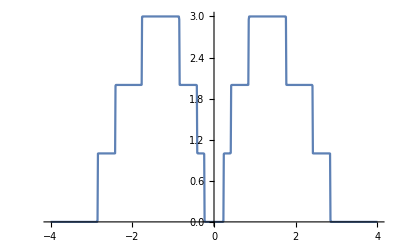

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
tr10[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],T=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},
Do[J=
Module[{c=
RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]],gg}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[T].J.T].c],100]; J=J]; Il1:=Inverse[IdentityMatrix[14]-sl1.TT[1].SR[ω,0.001,1,0].TT[1]].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];
η]
```

```mathematica
Timing[Mean[Table[tr10[1.5,0.0001,1,0,0.7],4000]]]
```

{146.025,0.377681}

```mathematica
Table[{ω,Mean[Table[tr3[ω,0.001,1,0,0.7],1500]]},{ω,Range[0,4,0.01]}]
```

$Aborted

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/"]]
```

```mathematica
StandardDeviation[Table[tr3[1.5,0.0001,1,0,0.7],2500]]
```

0.269769

```mathematica
StandardDeviation[%36]
```

0.369942

```mathematica
Mean[%36]
```

0.680313

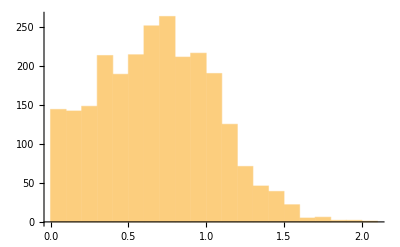

```mathematica
Histogram[%36]
```

```mathematica
test[ω_,δ_,t_,ϵ_,ϵ1_]:= Module[{J=IdentityMatrix[14]-IdentityMatrix[14],gg=β[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}],μ2=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2}}->ω+ⅈ*δ-ϵ1]],gg}]},J+c],2]; J=J]
```

```mathematica
MatrixForm[test[0,0,0,0,1]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
tr4[ω_,δ_,t_,ϵ_,ϵ1_,x_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,14}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],x];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.TT[1].SR[ω,δ,1,0].TT[1]].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl1.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η]
```

```mathematica
Table[{ω,Mean[Table[tr4[ω,0.001,1,0,0.7,8],1000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000169125},{0.01,0.000116832},{0.02,0.0000786958},{0.03,0.0000740119},{0.04,0.0000882002},{0.05,0.000105689},{0.06,0.000154905},{0.07,0.000207405},{0.08,0.000310193},{0.09,0.00039527},{0.1,0.000577687},{0.11,0.000700322},{0.12,0.000920383},{0.13,0.00122334},{0.14,0.001588},{0.15,0.00202503},{0.16,0.00246273},{0.17,0.00319007},{0.18,0.00420286},{0.19,0.00539722},{0.2,0.00771936},{0.21,0.011226},{0.22,0.0159735},{0.23,0.0293366},{0.24,0.0446149},{0.25,0.071634},{0.26,0.140319},{0.27,0.269463},{0.28,0.384188},{0.29,0.531066},{0.3,0.639628},{0.31,0.718461},{0.32,0.765752},{0.33,0.782938},{0.34,0.782731},{0.35,0.788148},{0.36,0.781441},{0.37,0.781315},{0.38,0.758244},{0.39,0.751881},{0.4,0.710023},{0.41,0.61474},{0.42,0.558854},{0.43,0.607738},{0.44,0.670474},{0.45,0.756939},{0.46,0.855205},{0.47,0.998566},{0.48,1.12968},{0.49,1.24677},{0.5,1.29632},{0.51,1.38266},{0.52,1.44866},{0.53,1.46166},{0.54,1.48716},{0.55,1.51387},{0.56,1.52856},{0.57,1.55147},{0.58,1.56553},{0.59,1.57632},{0.6,1.59338},{0.61,1.60554},{0.62,1.60923},{0.63,1.63147},{0.64,1.63208},{0.65,1.63642},{0.66,1.64868},{0.67,1.64199},{0.68,1.65716},{0.69,1.65964},{0.7,1.67145},{0.71,1.6666},{0.72,1.66601},{0.73,1.66139},{0.74,1.66808},{0.75,1.67492},{0.76,1.67367},{0.77,1.66975},{0.78,1.67924},{0.79,1.67371},{0.8,1.66599},{0.81,1.65182},{0.82,1.63309},{0.83,1.5888},{0.84,1.48639},{0.85,1.19977},{0.86,1.24795},{0.87,1.30223},{0.88,1.38138},{0.89,1.55214},{0.9,1.66406},{0.91,1.80986},{0.92,1.95682},{0.93,2.01585},{0.94,2.1055},{0.95,2.15331},{0.96,2.19798},{0.97,2.25512},{0.98,2.29366},{0.99,2.35566},{1.,2.37689},{1.01,2.40032},{1.02,2.40039},{1.03,2.37092},{1.04,2.25176},{1.05,2.0426},{1.06,1.66689},{1.07,1.22368},{1.08,0.887646},{1.09,0.712487},{1.1,0.716308},{1.11,0.853009},{1.12,1.00941},{1.13,1.14567},{1.14,1.2992},{1.15,1.38487},{1.16,1.4604},{1.17,1.53029},{1.18,1.59984},{1.19,1.63553},{1.2,1.70194},{1.21,1.73171},{1.22,1.75924},{1.23,1.78472},{1.24,1.81179},{1.25,1.81584},{1.26,1.82507},{1.27,1.86056},{1.28,1.85471},{1.29,1.86333},{1.3,1.87616},{1.31,1.86592},{1.32,1.8642},{1.33,1.8724},{1.34,1.87761},{1.35,1.88636},{1.36,1.88883},{1.37,1.8843},{1.38,1.87612},{1.39,1.88576},{1.4,1.87749},{1.41,1.88577},{1.42,1.873},{1.43,1.88381},{1.44,1.8804},{1.45,1.87457},{1.46,1.86408},{1.47,1.87092},{1.48,1.84315},{1.49,1.83034},{1.5,1.81485},{1.51,1.81927},{1.52,1.80998},{1.53,1.8005},{1.54,1.80102},{1.55,1.77679},{1.56,1.74996},{1.57,1.73437},{1.58,1.71865},{1.59,1.70645},{1.6,1.6785},{1.61,1.65216},{1.62,1.6388},{1.63,1.60914},{1.64,1.57954},{1.65,1.54057},{1.66,1.49433},{1.67,1.45469},{1.68,1.409},{1.69,1.348},{1.7,1.24018},{1.71,1.1929},{1.72,1.07299},{1.73,0.941329},{1.74,0.849178},{1.75,0.762169},{1.76,1.06131},{1.77,2.61228},{1.78,2.04843},{1.79,2.27602},{1.8,2.36327},{1.81,1.85382},{1.82,1.32642},{1.83,1.11597},{1.84,1.0411},{1.85,0.817333},{1.86,0.782658},{1.87,0.840758},{1.88,0.930475},{1.89,0.978289},{1.9,1.09917},{1.91,1.11906},{1.92,1.16313},{1.93,1.19417},{1.94,1.22743},{1.95,1.25084},{1.96,1.27767},{1.97,1.29071},{1.98,1.28977},{1.99,1.29326},{2.,1.29458},{2.01,1.32078},{2.02,1.31051},{2.03,1.32479},{2.04,1.32292},{2.05,1.31134},{2.06,1.32397},{2.07,1.32456},{2.08,1.32081},{2.09,1.31417},{2.1,1.3136},{2.11,1.3073},{2.12,1.30913},{2.13,1.30015},{2.14,1.30444},{2.15,1.29798},{2.16,1.29523},{2.17,1.27285},{2.18,1.2791},{2.19,1.25398},{2.2,1.26241},{2.21,1.25136},{2.22,1.22225},{2.23,1.21753},{2.24,1.21423},{2.25,1.19911},{2.26,1.17164},{2.27,1.16761},{2.28,1.17078},{2.29,1.13349},{2.3,1.12954},{2.31,1.10522},{2.32,1.09406},{2.33,1.05034},{2.34,1.03606},{2.35,0.987207},{2.36,0.971006},{2.37,0.88939},{2.38,0.845588},{2.39,0.754789},{2.4,0.639712},{2.41,0.630603},{2.42,1.46933},{2.43,1.55216},{2.44,1.35406},{2.45,1.25924},{2.46,1.15144},{2.47,0.927279},{2.48,0.649435},{2.49,0.579924},{2.5,0.46431},{2.51,0.463718},{2.52,0.498658},{2.53,0.501488},{2.54,0.502109},{2.55,0.519227},{2.56,0.56395},{2.57,0.563934},{2.58,0.568189},{2.59,0.591707},{2.6,0.602876},{2.61,0.603702},{2.62,0.603046},{2.63,0.612289},{2.64,0.612372},{2.65,0.609931},{2.66,0.619185},{2.67,0.605634},{2.68,0.608205},{2.69,0.616826},{2.7,0.622831},{2.71,0.613333},{2.72,0.61272},{2.73,0.60202},{2.74,0.61346},{2.75,0.589607},{2.76,0.560391},{2.77,0.560743},{2.78,0.543032},{2.79,0.540405},{2.8,0.53885},{2.81,0.497312},{2.82,0.45264},{2.83,0.404603},{2.84,0.325049},{2.85,0.777654},{2.86,1.52467},{2.87,1.75003},{2.88,1.07091},{2.89,0.774463},{2.9,0.453669},{2.91,0.454538},{2.92,0.113661},{2.93,0.0597778},{2.94,0.0303472},{2.95,0.0124362},{2.96,0.00855704},{2.97,0.00701216},{2.98,0.00500576},{2.99,0.00390169},{3.,0.00297108},{3.01,0.00277673},{3.02,0.00210093},{3.03,0.00190955},{3.04,0.00142789},{3.05,0.00128363},{3.06,0.00116531},{3.07,0.00113043},{3.08,0.000844918},{3.09,0.000801027},{3.1,0.000764628},{3.11,0.000646599},{3.12,0.00058861},{3.13,0.000482058},{3.14,0.000445706},{3.15,0.000421213},{3.16,0.000384524},{3.17,0.00034201},{3.18,0.000326781},{3.19,0.000279011},{3.2,0.000286995},{3.21,0.000216043},{3.22,0.000203136},{3.23,0.000179856},{3.24,0.000154262},{3.25,0.000150868},{3.26,0.00014434},{3.27,0.000135953},{3.28,0.000114578},{3.29,0.000116722},{3.3,0.000100531},{3.31,0.0000876778},{3.32,0.0000930203},{3.33,0.0000870713},{3.34,0.0000765068},{3.35,0.0000775674},{3.36,0.0000687198},{3.37,0.0000688247},{3.38,0.0000686614},{3.39,0.0000569307},{3.4,0.0000543697},{3.41,0.0000454395},{3.42,0.0000468006},{3.43,0.0000426289},{3.44,0.0000393583},{3.45,0.0000380032},{3.46,0.0000376727},{3.47,0.0000336848},{3.48,0.000031084},{3.49,0.000027339},{3.5,0.000032437},{3.51,0.0000282414},{3.52,0.0000232974},{3.53,0.0000239459},{3.54,0.000023288},{3.55,0.0000197231},{3.56,0.0000199917},{3.57,0.0000186698},{3.58,0.0000173342},{3.59,0.0000180756},{3.6,0.0000159532},{3.61,0.0000160093},{3.62,0.0000141355},{3.63,0.0000149578},{3.64,0.0000132509},{3.65,0.0000114469},{3.66,0.0000120439},{3.67,0.0000122315},{3.68,0.0000109774},{3.69,0.0000114423},{3.7,9.8951×10^-6},{3.71,9.52432×10^-6},{3.72,9.07167×10^-6},{3.73,9.56682×10^-6},{3.74,7.16794×10^-6},{3.75,7.31258×10^-6},{3.76,6.5146×10^-6},{3.77,7.3132×10^-6},{3.78,7.674×10^-6},{3.79,6.26997×10^-6},{3.8,5.76589×10^-6},{3.81,5.32185×10^-6},{3.82,6.08228×10^-6},{3.83,5.60482×10^-6},{3.84,5.4994×10^-6},{3.85,4.7617×10^-6},{3.86,3.94215×10^-6},{3.87,4.50601×10^-6},{3.88,4.83255×10^-6},{3.89,3.93135×10^-6},{3.9,4.25315×10^-6},{3.91,3.77033×10^-6},{3.92,3.63909×10^-6},{3.93,3.54769×10^-6},{3.94,3.04641×10^-6},{3.95,3.34691×10^-6},{3.96,3.17304×10^-6},{3.97,2.93269×10^-6},{3.98,2.99688×10^-6},{3.99,2.84879×10^-6},{4.,2.72456×10^-6}}

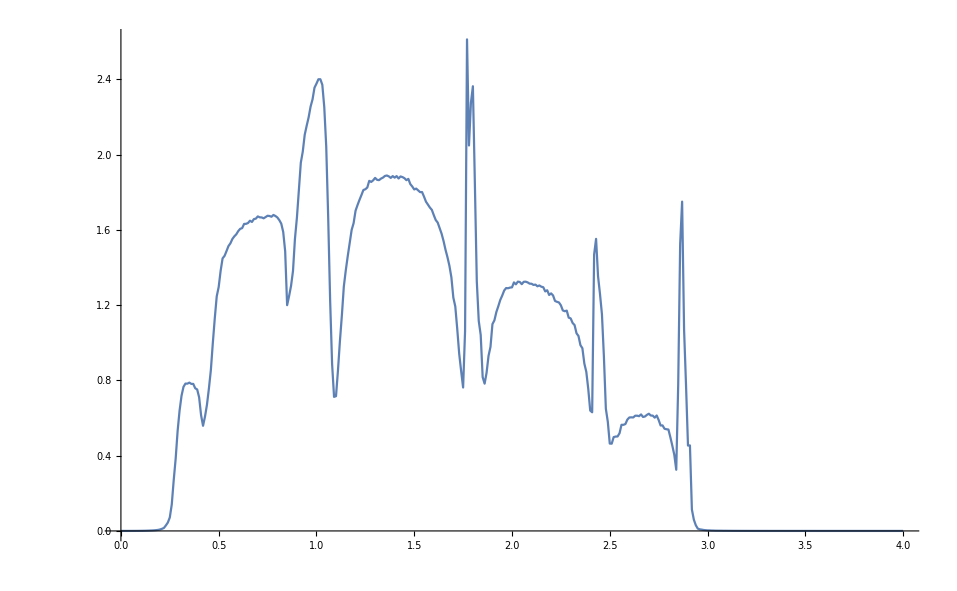

```mathematica
ListPlot[%96,Joined->True]
```

```mathematica
Table[{ω,Mean[Table[tr4[ω,0.001,1,0,0.7,8],1000]]},{ω,Range[0,4,0.01]}]
```

```mathematica
tr5[ω_,δ_,t_,ϵ_,ϵ1_,x_]:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]],Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],4];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.TT[1].SR[ω,δ,1,0].TT[1]].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl1.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η]
```

```mathematica
Timing[Mean[Table[tr5[2,0.001,1,0,0.7,0],2500]]]
```

{4.48307,0.952512}

```mathematica
Table[{ω,Mean[Table[tr5[ω,0.001,1,0,0.7,0],1000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.012018},{0.01,0.00825655},{0.02,0.00730401},{0.03,0.00561861},{0.04,0.00524222},{0.05,0.00385299},{0.06,0.00361792},{0.07,0.00273635},{0.08,0.00242808},{0.09,0.00219351},{0.1,0.00173748},{0.11,0.00183302},{0.12,0.00174931},{0.13,0.00171744},{0.14,0.00167281},{0.15,0.0019137},{0.16,0.00218379},{0.17,0.00249387},{0.18,0.00283271},{0.19,0.00375492},{0.2,0.00463593},{0.21,0.00611432},{0.22,0.00750505},{0.23,0.0120595},{0.24,0.0148956},{0.25,0.0258212},{0.26,0.0443782},{0.27,0.0650615},{0.28,0.0878599},{0.29,0.117323},{0.3,0.1503},{0.31,0.183155},{0.32,0.21096},{0.33,0.248243},{0.34,0.296402},{0.35,0.351685},{0.36,0.383878},{0.37,0.428097},{0.38,0.453637},{0.39,0.481617},{0.4,0.50111},{0.41,0.520388},{0.42,0.518251},{0.43,0.537825},{0.44,0.578598},{0.45,0.607948},{0.46,0.652611},{0.47,0.693579},{0.48,0.726998},{0.49,0.756519},{0.5,0.77644},{0.51,0.815468},{0.52,0.851433},{0.53,0.890287},{0.54,0.930321},{0.55,0.972412},{0.56,0.987722},{0.57,1.03033},{0.58,1.07237},{0.59,1.10486},{0.6,1.1305},{0.61,1.17075},{0.62,1.20785},{0.63,1.24372},{0.64,1.26914},{0.65,1.29415},{0.66,1.30953},{0.67,1.32203},{0.68,1.35189},{0.69,1.35103},{0.7,1.3827},{0.71,1.39022},{0.72,1.40755},{0.73,1.40531},{0.74,1.41274},{0.75,1.41376},{0.76,1.42593},{0.77,1.41696},{0.78,1.41813},{0.79,1.41629},{0.8,1.40555},{0.81,1.37978},{0.82,1.36065},{0.83,1.34991},{0.84,1.28081},{0.85,1.16061},{0.86,1.19586},{0.87,1.21048},{0.88,1.2243},{0.89,1.25258},{0.9,1.27617},{0.91,1.33046},{0.92,1.33723},{0.93,1.36407},{0.94,1.38795},{0.95,1.44711},{0.96,1.47615},{0.97,1.50345},{0.98,1.5415},{0.99,1.57144},{1.,1.65083},{1.01,1.68034},{1.02,1.72959},{1.03,1.7458},{1.04,1.7709},{1.05,1.70063},{1.06,1.57018},{1.07,1.4328},{1.08,1.27165},{1.09,1.14544},{1.1,1.17493},{1.11,1.18077},{1.12,1.20395},{1.13,1.2128},{1.14,1.20373},{1.15,1.18819},{1.16,1.1319},{1.17,1.05134},{1.18,1.01347},{1.19,1.01182},{1.2,0.995615},{1.21,1.01985},{1.22,1.07806},{1.23,1.08633},{1.24,1.12117},{1.25,1.13506},{1.26,1.17507},{1.27,1.23414},{1.28,1.26847},{1.29,1.28748},{1.3,1.31934},{1.31,1.35061},{1.32,1.36652},{1.33,1.38036},{1.34,1.43914},{1.35,1.4475},{1.36,1.45866},{1.37,1.49927},{1.38,1.5186},{1.39,1.52118},{1.4,1.54241},{1.41,1.56765},{1.42,1.57615},{1.43,1.59886},{1.44,1.59225},{1.45,1.58092},{1.46,1.58366},{1.47,1.58157},{1.48,1.5792},{1.49,1.58772},{1.5,1.57776},{1.51,1.57568},{1.52,1.55778},{1.53,1.55177},{1.54,1.52986},{1.55,1.53567},{1.56,1.52177},{1.57,1.51052},{1.58,1.49906},{1.59,1.47462},{1.6,1.44808},{1.61,1.46359},{1.62,1.39594},{1.63,1.39973},{1.64,1.36202},{1.65,1.34046},{1.66,1.31273},{1.67,1.27906},{1.68,1.24415},{1.69,1.19998},{1.7,1.13173},{1.71,1.05113},{1.72,1.01875},{1.73,0.942971},{1.74,0.886904},{1.75,0.801911},{1.76,0.919429},{1.77,2.06104},{1.78,1.95325},{1.79,1.81532},{1.8,1.79276},{1.81,1.53989},{1.82,1.48988},{1.83,1.36823},{1.84,1.36319},{1.85,1.17292},{1.86,1.27943},{1.87,1.2696},{1.88,1.19659},{1.89,1.19161},{1.9,1.03752},{1.91,1.02547},{1.92,0.929878},{1.93,0.865997},{1.94,0.804038},{1.95,0.806511},{1.96,0.833715},{1.97,0.827188},{1.98,0.876479},{1.99,0.926748},{2.,0.959262},{2.01,1.00242},{2.02,1.017},{2.03,1.10141},{2.04,1.11503},{2.05,1.12772},{2.06,1.16814},{2.07,1.19397},{2.08,1.21565},{2.09,1.24461},{2.1,1.23518},{2.11,1.24405},{2.12,1.25365},{2.13,1.25307},{2.14,1.25181},{2.15,1.2814},{2.16,1.26071},{2.17,1.26513},{2.18,1.26131},{2.19,1.25111},{2.2,1.27025},{2.21,1.26325},{2.22,1.25937},{2.23,1.2406},{2.24,1.24942},{2.25,1.24617},{2.26,1.23992},{2.27,1.22104},{2.28,1.2054},{2.29,1.19263},{2.3,1.17539},{2.31,1.16073},{2.32,1.14314},{2.33,1.11259},{2.34,1.09725},{2.35,1.08045},{2.36,1.03154},{2.37,1.0138},{2.38,0.955292},{2.39,0.869024},{2.4,0.763278},{2.41,0.602027},{2.42,1.30535},{2.43,1.05034},{2.44,0.950143},{2.45,0.802945},{2.46,0.963747},{2.47,0.894599},{2.48,1.00697},{2.49,1.03511},{2.5,1.32981},{2.51,1.145},{2.52,1.09152},{2.53,0.975834},{2.54,0.831772},{2.55,0.777832},{2.56,0.710171},{2.57,0.600604},{2.58,0.619087},{2.59,0.605537},{2.6,0.591446},{2.61,0.584262},{2.62,0.580946},{2.63,0.589846},{2.64,0.64175},{2.65,0.623426},{2.66,0.652294},{2.67,0.668343},{2.68,0.662166},{2.69,0.651411},{2.7,0.645972},{2.71,0.64852},{2.72,0.634883},{2.73,0.611611},{2.74,0.609847},{2.75,0.594316},{2.76,0.580906},{2.77,0.57332},{2.78,0.56009},{2.79,0.541374},{2.8,0.5412},{2.81,0.515255},{2.82,0.488047},{2.83,0.419358},{2.84,0.327277},{2.85,1.87951},{2.86,2.24216},{2.87,0.926513},{2.88,0.5608},{2.89,0.738344},{2.9,0.413539},{2.91,1.30577},{2.92,1.71129},{2.93,0.871654},{2.94,1.10184},{2.95,0.52677},{2.96,0.482196},{2.97,0.249611},{2.98,0.171214},{2.99,0.201639},{3.,0.0914511},{3.01,0.100169},{3.02,0.0724015},{3.03,0.0778168},{3.04,0.0315811},{3.05,0.0540255},{3.06,0.0279897},{3.07,0.0112685},{3.08,0.00997959},{3.09,0.00681679},{3.1,0.00365858},{3.11,0.00353326},{3.12,0.00201878},{3.13,0.00166177},{3.14,0.00150933},{3.15,0.00130963},{3.16,0.00107285},{3.17,0.000998686},{3.18,0.000920127},{3.19,0.000819304},{3.2,0.000732138},{3.21,0.000651395},{3.22,0.000604906},{3.23,0.0005412},{3.24,0.000497327},{3.25,0.000444072},{3.26,0.000418191},{3.27,0.000377957},{3.28,0.000349713},{3.29,0.00030671},{3.3,0.000298587},{3.31,0.000246317},{3.32,0.000256665},{3.33,0.000216984},{3.34,0.000219136},{3.35,0.000201464},{3.36,0.000185209},{3.37,0.000168687},{3.38,0.000152314},{3.39,0.000149338},{3.4,0.000139483},{3.41,0.000122031},{3.42,0.000121632},{3.43,0.000116788},{3.44,0.00010135},{3.45,0.0000975638},{3.46,0.0000905157},{3.47,0.0000833456},{3.48,0.0000881256},{3.49,0.0000807915},{3.5,0.0000750687},{3.51,0.0000699419},{3.52,0.0000624865},{3.53,0.0000625489},{3.54,0.000057935},{3.55,0.0000573269},{3.56,0.0000519326},{3.57,0.0000471982},{3.58,0.0000460892},{3.59,0.0000444255},{3.6,0.0000413359},{3.61,0.0000387268},{3.62,0.0000352039},{3.63,0.0000358179},{3.64,0.0000331605},{3.65,0.0000316451},{3.66,0.0000288004},{3.67,0.0000279961},{3.68,0.0000273092},{3.69,0.0000249224},{3.7,0.0000253268},{3.71,0.0000239762},{3.72,0.000023324},{3.73,0.0000213296},{3.74,0.0000211202},{3.75,0.0000183125},{3.76,0.0000193003},{3.77,0.0000173711},{3.78,0.0000169949},{3.79,0.0000156014},{3.8,0.0000159032},{3.81,0.0000150946},{3.82,0.0000146182},{3.83,0.0000131148},{3.84,0.0000130803},{3.85,0.0000123131},{3.86,0.0000117309},{3.87,0.0000116281},{3.88,0.0000112368},{3.89,0.0000102485},{3.9,9.95129×10^-6},{3.91,9.5323×10^-6},{3.92,8.55544×10^-6},{3.93,8.61948×10^-6},{3.94,8.77022×10^-6},{3.95,7.7049×10^-6},{3.96,7.97137×10^-6},{3.97,7.04306×10^-6},{3.98,7.2435×10^-6},{3.99,6.81174×10^-6},{4.,6.52383×10^-6}}

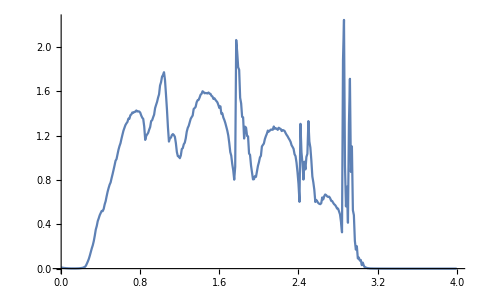

```mathematica
ListPlot[%107,Joined->True]
```

```mathematica
Table[{ω,Mean[Table[tr5[ω,0.001,1,0,0.7,0],2500]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0115649},{0.01,0.00846371},{0.02,0.00712641},{0.03,0.00582716},{0.04,0.00500065},{0.05,0.00427809},{0.06,0.00346866},{0.07,0.00277916},{0.08,0.00252434},{0.09,0.00224467},{0.1,0.00201888},{0.11,0.00174637},{0.12,0.00168633},{0.13,0.00176759},{0.14,0.00180766},{0.15,0.00194045},{0.16,0.00219113},{0.17,0.00252107},{0.18,0.00289894},{0.19,0.00357787},{0.2,0.00460154},{0.21,0.00587235},{0.22,0.00777924},{0.23,0.0114953},{0.24,0.0147533},{0.25,0.0277776},{0.26,0.0442676},{0.27,0.0670321},{0.28,0.0923463},{0.29,0.114353},{0.3,0.148844},{0.31,0.181274},{0.32,0.218149},{0.33,0.249974},{0.34,0.298389},{0.35,0.343556},{0.36,0.382224},{0.37,0.419144},{0.38,0.449701},{0.39,0.479573},{0.4,0.498567},{0.41,0.511332},{0.42,0.511724},{0.43,0.547675},{0.44,0.573373},{0.45,0.610012},{0.46,0.657463},{0.47,0.684904},{0.48,0.722176},{0.49,0.752876},{0.5,0.788259},{0.51,0.817546},{0.52,0.859988},{0.53,0.891668},{0.54,0.930161},{0.55,0.962811},{0.56,1.00441},{0.57,1.03549},{0.58,1.063},{0.59,1.0993},{0.6,1.14184},{0.61,1.16769},{0.62,1.19883},{0.63,1.2393},{0.64,1.25494},{0.65,1.28526},{0.66,1.30299},{0.67,1.33002},{0.68,1.34184},{0.69,1.35934},{0.7,1.37682},{0.71,1.38274},{0.72,1.39975},{0.73,1.41335},{0.74,1.41511},{0.75,1.41858},{0.76,1.42053},{0.77,1.4118},{0.78,1.41542},{0.79,1.41271},{0.8,1.40529},{0.81,1.38979},{0.82,1.36897},{0.83,1.32455},{0.84,1.27073},{0.85,1.15373},{0.86,1.18804},{0.87,1.21515},{0.88,1.24108},{0.89,1.27171},{0.9,1.28943},{0.91,1.31044},{0.92,1.3272},{0.93,1.34765},{0.94,1.40175},{0.95,1.43042},{0.96,1.46694},{0.97,1.50212},{0.98,1.54642},{0.99,1.59102},{1.,1.64001},{1.01,1.67488},{1.02,1.72202},{1.03,1.75694},{1.04,1.74353},{1.05,1.69622},{1.06,1.60409},{1.07,1.42503},{1.08,1.27006},{1.09,1.17672},{1.1,1.16698},{1.11,1.19135},{1.12,1.20605},{1.13,1.19728},{1.14,1.19898},{1.15,1.19183},{1.16,1.10573},{1.17,1.06936},{1.18,1.02339},{1.19,0.959668},{1.2,0.994048},{1.21,1.02613},{1.22,1.05489},{1.23,1.07811},{1.24,1.11822},{1.25,1.15851},{1.26,1.19232},{1.27,1.24016},{1.28,1.24695},{1.29,1.28525},{1.3,1.29815},{1.31,1.32767},{1.32,1.36546},{1.33,1.40803},{1.34,1.42742},{1.35,1.48351},{1.36,1.48665},{1.37,1.50362},{1.38,1.52713},{1.39,1.5274},{1.4,1.55185},{1.41,1.56773},{1.42,1.57436},{1.43,1.58426},{1.44,1.5872},{1.45,1.57811},{1.46,1.59514},{1.47,1.59365},{1.48,1.5859},{1.49,1.56908},{1.5,1.56238},{1.51,1.5676},{1.52,1.56334},{1.53,1.54945},{1.54,1.54855},{1.55,1.53889},{1.56,1.53378},{1.57,1.49583},{1.58,1.49611},{1.59,1.48108},{1.6,1.44368},{1.61,1.4369},{1.62,1.41544},{1.63,1.40448},{1.64,1.35102},{1.65,1.33739},{1.66,1.29941},{1.67,1.25617},{1.68,1.2281},{1.69,1.17099},{1.7,1.1277},{1.71,1.05968},{1.72,1.01259},{1.73,0.940861},{1.74,0.885508},{1.75,0.829887},{1.76,0.908176},{1.77,1.9984},{1.78,2.07781},{1.79,1.92549},{1.8,1.70051},{1.81,1.59372},{1.82,1.46975},{1.83,1.40204},{1.84,1.34999},{1.85,1.46083},{1.86,1.31077},{1.87,1.27144},{1.88,1.23533},{1.89,1.11752},{1.9,1.03909},{1.91,0.998402},{1.92,0.964726},{1.93,0.90229},{1.94,0.882838},{1.95,0.824349},{1.96,0.842059},{1.97,0.823929},{1.98,0.870292},{1.99,0.916987},{2.,0.954661},{2.01,0.9789},{2.02,1.03685},{2.03,1.08829},{2.04,1.11539},{2.05,1.14361},{2.06,1.17622},{2.07,1.19381},{2.08,1.21191},{2.09,1.22194},{2.1,1.241},{2.11,1.24764},{2.12,1.24747},{2.13,1.25304},{2.14,1.24988},{2.15,1.26172},{2.16,1.27122},{2.17,1.26308},{2.18,1.27473},{2.19,1.27918},{2.2,1.26601},{2.21,1.26696},{2.22,1.26144},{2.23,1.26754},{2.24,1.25529},{2.25,1.24609},{2.26,1.22906},{2.27,1.21549},{2.28,1.2085},{2.29,1.20231},{2.3,1.16548},{2.31,1.15188},{2.32,1.14278},{2.33,1.11827},{2.34,1.097},{2.35,1.07133},{2.36,1.04126},{2.37,0.994126},{2.38,0.950291},{2.39,0.857444},{2.4,0.743235},{2.41,0.591715},{2.42,1.29442},{2.43,1.24295},{2.44,0.978926},{2.45,0.821412},{2.46,0.900443},{2.47,1.03585},{2.48,0.987203},{2.49,1.02828},{2.5,1.1817},{2.51,1.12976},{2.52,1.05916},{2.53,1.03226},{2.54,0.868099},{2.55,0.796207},{2.56,0.741833},{2.57,0.661294},{2.58,0.659883},{2.59,0.613055},{2.6,0.591214},{2.61,0.581158},{2.62,0.573072},{2.63,0.599271},{2.64,0.595802},{2.65,0.644188},{2.66,0.643394},{2.67,0.655368},{2.68,0.643515},{2.69,0.650008},{2.7,0.652029},{2.71,0.645451},{2.72,0.632758},{2.73,0.621436},{2.74,0.60897},{2.75,0.592369},{2.76,0.586757},{2.77,0.568419},{2.78,0.557215},{2.79,0.539716},{2.8,0.53261},{2.81,0.509747},{2.82,0.474955},{2.83,0.422502},{2.84,0.327404},{2.85,2.39136},{2.86,1.86742},{2.87,0.765273},{2.88,0.629695},{2.89,0.546202},{2.9,0.590265},{2.91,1.21492},{2.92,1.08837},{2.93,0.949499},{2.94,1.14994},{2.95,0.882584},{2.96,0.557819},{2.97,0.342484},{2.98,0.30586},{2.99,0.124698},{3.,0.126359},{3.01,0.103863},{3.02,0.124694},{3.03,0.0729295},{3.04,0.0482708},{3.05,0.0448276},{3.06,0.0284644},{3.07,0.0218903},{3.08,0.00835618},{3.09,0.00540162},{3.1,0.00312591},{3.11,0.00253899},{3.12,0.00206702},{3.13,0.0017189},{3.14,0.00150358},{3.15,0.00133482},{3.16,0.00118525},{3.17,0.00100009},{3.18,0.000919809},{3.19,0.000801278},{3.2,0.000721443},{3.21,0.000658837},{3.22,0.000605808},{3.23,0.000553243},{3.24,0.000490978},{3.25,0.000464353},{3.26,0.000419655},{3.27,0.000380456},{3.28,0.000354611},{3.29,0.000317043},{3.3,0.000297875},{3.31,0.000264434},{3.32,0.000239511},{3.33,0.000232306},{3.34,0.000215729},{3.35,0.000204286},{3.36,0.00018375},{3.37,0.000177457},{3.38,0.000163077},{3.39,0.000146899},{3.4,0.000140895},{3.41,0.000125824},{3.42,0.00012274},{3.43,0.00011189},{3.44,0.000103115},{3.45,0.000101054},{3.46,0.00009186},{3.47,0.0000857891},{3.48,0.000081277},{3.49,0.0000744315},{3.5,0.0000744893},{3.51,0.0000680247},{3.52,0.000064424},{3.53,0.0000608108},{3.54,0.0000570866},{3.55,0.0000561273},{3.56,0.0000517137},{3.57,0.0000482952},{3.58,0.0000464907},{3.59,0.0000432851},{3.6,0.0000398775},{3.61,0.0000386407},{3.62,0.0000362656},{3.63,0.0000357398},{3.64,0.0000331264},{3.65,0.0000304218},{3.66,0.0000310115},{3.67,0.0000289962},{3.68,0.0000277651},{3.69,0.0000263693},{3.7,0.0000237958},{3.71,0.0000242366},{3.72,0.0000223538},{3.73,0.0000214429},{3.74,0.0000199156},{3.75,0.000019696},{3.76,0.0000194025},{3.77,0.000017772},{3.78,0.0000176127},{3.79,0.0000162363},{3.8,0.0000151795},{3.81,0.0000147056},{3.82,0.0000144379},{3.83,0.0000134365},{3.84,0.0000124725},{3.85,0.0000125624},{3.86,0.0000116641},{3.87,0.00001155},{3.88,0.0000105453},{3.89,0.0000104557},{3.9,9.76504×10^-6},{3.91,9.40658×10^-6},{3.92,9.0438×10^-6},{3.93,8.58276×10^-6},{3.94,8.42959×10^-6},{3.95,7.87762×10^-6},{3.96,7.95792×10^-6},{3.97,7.30631×10^-6},{3.98,7.15989×10^-6},{3.99,6.66628×10^-6},{4.,6.41117×10^-6}}

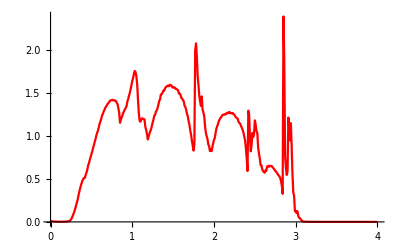

```mathematica
ListLinePlot[%111,PlotStyle->Red]
```

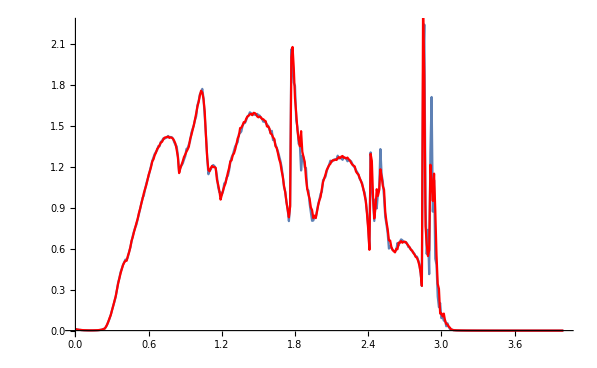

```mathematica
Show[%108,%112]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{},A:=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];B:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η];Y:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η];R:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η];(A+B+Y+R)/4]
```

```mathematica
Timing[Mean[Table[tr[0,0.001,1,0,0.2,1],2000]]]
```

{11.4842,0.0000295645}

```mathematica
Export["11imp7.csv",Table[{ω,Mean[Table[tr[ω,0.001,1,0,0.7],1500]]},{ω,Range[0,4,0.01]}]]
```

11imp7.csv

```mathematica
Export["11imp5.csv",Table[{ω,Mean[Table[tr[ω,0.001,1,0,0.5],1500]]},{ω,Range[0,4,0.01]}]]
```

11imp5.csv

```mathematica
Export["11imp3.csv",Table[{ω,Mean[Table[tr[ω,0.001,1,0,0.3],1500]]},{ω,Range[0,4,0.01]}]]
```

11imp3.csv

```mathematica
Export["11imp9.csv",Table[{ω,Mean[Table[tr[ω,0.001,1,0,0.9],1500]]},{ω,Range[0,4,0.01]}]]
```

11imp9.csv

```mathematica
Import["11imp9.csv"]
```

{{0.,0.0967716},{0.01,0.0591222},{0.02,0.0328022},{0.03,0.0213423},{0.04,0.01816},{0.05,0.0137714},{0.06,0.0112535},{0.07,0.00955281},{0.08,0.00836347},{0.09,0.00735207},{0.1,0.00645342},{0.11,0.00540721},{0.12,0.00503771},{0.13,0.004794},{0.14,0.00452452},{0.15,0.00455219},{0.16,0.00451383},{0.17,0.00494605},{0.18,0.00533238},{0.19,0.00599159},{0.2,0.00696962},{0.21,0.00819338},{0.22,0.0107853},{0.23,0.0143499},{0.24,0.0165181},{0.25,0.0232195},{0.26,0.0346659},{0.27,0.0479967},{0.28,0.0634516},{0.29,0.0826665},{0.3,0.102},{0.31,0.125103},{0.32,0.148693},{0.33,0.179819},{0.34,0.207878},{0.35,0.247952},{0.36,0.282621},{0.37,0.319743},{0.38,0.349555},{0.39,0.382257},{0.4,0.408411},{0.41,0.438739},{0.42,0.458866},{0.43,0.473508},{0.44,0.488825},{0.45,0.511339},{0.46,0.534114},{0.47,0.566588},{0.48,0.589647},{0.49,0.616322},{0.5,0.640029},{0.51,0.668014},{0.52,0.688448},{0.53,0.719776},{0.54,0.756358},{0.55,0.777319},{0.56,0.804277},{0.57,0.831963},{0.58,0.862604},{0.59,0.893843},{0.6,0.920517},{0.61,0.947996},{0.62,0.975761},{0.63,1.00589},{0.64,1.03059},{0.65,1.05147},{0.66,1.08328},{0.67,1.09945},{0.68,1.12482},{0.69,1.14742},{0.7,1.15528},{0.71,1.17386},{0.72,1.18881},{0.73,1.19753},{0.74,1.20914},{0.75,1.21132},{0.76,1.21433},{0.77,1.22486},{0.78,1.21088},{0.79,1.20892},{0.8,1.20316},{0.81,1.18477},{0.82,1.15606},{0.83,1.12553},{0.84,1.05239},{0.85,0.956929},{0.86,0.993983},{0.87,1.00528},{0.88,1.03849},{0.89,1.05532},{0.9,1.08054},{0.91,1.10538},{0.92,1.12317},{0.93,1.15616},{0.94,1.18458},{0.95,1.20468},{0.96,1.22494},{0.97,1.25505},{0.98,1.29016},{0.99,1.33616},{1.,1.36045},{1.01,1.40391},{1.02,1.43954},{1.03,1.45741},{1.04,1.47703},{1.05,1.47228},{1.06,1.43794},{1.07,1.35309},{1.08,1.24188},{1.09,1.12201},{1.1,1.02513},{1.11,0.969371},{1.12,0.923203},{1.13,0.90709},{1.14,0.90519},{1.15,0.906415},{1.16,0.932637},{1.17,0.94224},{1.18,0.94368},{1.19,0.922272},{1.2,0.919642},{1.21,0.889138},{1.22,0.84393},{1.23,0.829418},{1.24,0.813386},{1.25,0.801294},{1.26,0.806945},{1.27,0.806129},{1.28,0.817117},{1.29,0.842021},{1.3,0.854767},{1.31,0.873868},{1.32,0.904078},{1.33,0.9297},{1.34,0.95032},{1.35,0.953458},{1.36,0.97312},{1.37,0.989777},{1.38,0.993028},{1.39,1.00375},{1.4,1.01645},{1.41,1.0272},{1.42,1.03819},{1.43,1.04204},{1.44,1.06697},{1.45,1.07033},{1.46,1.08839},{1.47,1.09855},{1.48,1.09092},{1.49,1.09277},{1.5,1.10863},{1.51,1.09332},{1.52,1.10279},{1.53,1.08721},{1.54,1.09788},{1.55,1.08468},{1.56,1.073},{1.57,1.06597},{1.58,1.0482},{1.59,1.03153},{1.6,1.02356},{1.61,1.01033},{1.62,0.985241},{1.63,0.964805},{1.64,0.947538},{1.65,0.914689},{1.66,0.871996},{1.67,0.846374},{1.68,0.810409},{1.69,0.786257},{1.7,0.758786},{1.71,0.730655},{1.72,0.688482},{1.73,0.678509},{1.74,0.678949},{1.75,0.749742},{1.76,1.00743},{1.77,1.87919},{1.78,1.77485},{1.79,1.77701},{1.8,1.74366},{1.81,1.60972},{1.82,1.56347},{1.83,1.40935},{1.84,1.31089},{1.85,1.34473},{1.86,1.20927},{1.87,1.18188},{1.88,1.16322},{1.89,1.12272},{1.9,1.07761},{1.91,1.03306},{1.92,0.991191},{1.93,0.947636},{1.94,0.925701},{1.95,0.87578},{1.96,0.82057},{1.97,0.793473},{1.98,0.789603},{1.99,0.705621},{2.,0.714508},{2.01,0.692362},{2.02,0.680795},{2.03,0.692912},{2.04,0.672034},{2.05,0.69094},{2.06,0.68902},{2.07,0.711336},{2.08,0.729242},{2.09,0.758052},{2.1,0.760252},{2.11,0.782224},{2.12,0.790858},{2.13,0.820351},{2.14,0.837363},{2.15,0.850544},{2.16,0.874249},{2.17,0.869941},{2.18,0.886052},{2.19,0.896263},{2.2,0.893987},{2.21,0.899666},{2.22,0.90285},{2.23,0.910906},{2.24,0.908116},{2.25,0.906212},{2.26,0.906026},{2.27,0.890603},{2.28,0.894194},{2.29,0.871833},{2.3,0.869555},{2.31,0.851335},{2.32,0.83716},{2.33,0.819448},{2.34,0.79667},{2.35,0.778108},{2.36,0.747905},{2.37,0.709711},{2.38,0.663278},{2.39,0.610641},{2.4,0.544406},{2.41,0.533058},{2.42,1.08293},{2.43,1.10469},{2.44,1.22941},{2.45,1.14353},{2.46,1.10437},{2.47,1.0101},{2.48,0.8872},{2.49,0.828797},{2.5,0.892765},{2.51,0.815072},{2.52,0.869324},{2.53,0.913055},{2.54,0.874478},{2.55,0.916912},{2.56,0.943239},{2.57,0.864177},{2.58,0.89268},{2.59,0.836259},{2.6,0.843115},{2.61,0.809572},{2.62,0.787692},{2.63,0.685178},{2.64,0.633436},{2.65,0.579926},{2.66,0.528569},{2.67,0.534755},{2.68,0.506783},{2.69,0.494916},{2.7,0.487364},{2.71,0.477022},{2.72,0.476567},{2.73,0.47024},{2.74,0.466349},{2.75,0.464767},{2.76,0.447139},{2.77,0.427624},{2.78,0.408649},{2.79,0.383339},{2.8,0.35719},{2.81,0.319104},{2.82,0.287491},{2.83,0.256789},{2.84,0.272315},{2.85,2.374},{2.86,5.68896},{2.87,5.45907},{2.88,4.69673},{2.89,3.17566},{2.9,2.448},{2.91,1.72736},{2.92,1.45436},{2.93,1.11583},{2.94,1.04048},{2.95,1.08775},{2.96,1.01685},{2.97,1.23095},{2.98,1.15799},{2.99,1.24296},{3.,1.03807},{3.01,0.820513},{3.02,0.6088},{3.03,0.427242},{3.04,0.327568},{3.05,0.240249},{3.06,0.218196},{3.07,0.207741},{3.08,0.139922},{3.09,0.0833124},{3.1,0.07008},{3.11,0.0512254},{3.12,0.0623545},{3.13,0.0248326},{3.14,0.0209135},{3.15,0.0115875},{3.16,0.0107808},{3.17,0.0093667},{3.18,0.00356082},{3.19,0.00340919},{3.2,0.00287576},{3.21,0.00194262},{3.22,0.00154822},{3.23,0.00147726},{3.24,0.00125468},{3.25,0.00109915},{3.26,0.00098923},{3.27,0.000908971},{3.28,0.000834395},{3.29,0.000758213},{3.3,0.000679866},{3.31,0.000614112},{3.32,0.000566684},{3.33,0.000518985},{3.34,0.000470023},{3.35,0.000436368},{3.36,0.000405758},{3.37,0.000379114},{3.38,0.00035747},{3.39,0.000320599},{3.4,0.000294189},{3.41,0.000281862},{3.42,0.000256186},{3.43,0.000244015},{3.44,0.000226518},{3.45,0.0002134},{3.46,0.000198488},{3.47,0.000180853},{3.48,0.000172159},{3.49,0.000158364},{3.5,0.000153105},{3.51,0.000144049},{3.52,0.000134379},{3.53,0.000123305},{3.54,0.000117972},{3.55,0.000111841},{3.56,0.000106832},{3.57,0.000100535},{3.58,0.0000938174},{3.59,0.0000891988},{3.6,0.0000852025},{3.61,0.0000778835},{3.62,0.000075327},{3.63,0.0000711552},{3.64,0.0000667044},{3.65,0.0000639156},{3.66,0.0000615369},{3.67,0.0000581354},{3.68,0.0000540472},{3.69,0.0000516391},{3.7,0.0000488451},{3.71,0.0000473772},{3.72,0.0000448206},{3.73,0.0000414819},{3.74,0.0000399132},{3.75,0.0000373735},{3.76,0.0000362818},{3.77,0.0000339195},{3.78,0.0000330451},{3.79,0.0000310968},{3.8,0.0000305503},{3.81,0.0000287928},{3.82,0.0000269997},{3.83,0.0000253071},{3.84,0.0000245684},{3.85,0.0000236074},{3.86,0.0000223231},{3.87,0.0000218121},{3.88,0.000020468},{3.89,0.0000194702},{3.9,0.0000190143},{3.91,0.0000179424},{3.92,0.0000175106},{3.93,0.0000166981},{3.94,0.0000159942},{3.95,0.0000154762},{3.96,0.0000144099},{3.97,0.0000142289},{3.98,0.0000134643},{3.99,0.0000128864},{4.,0.0000122982}}

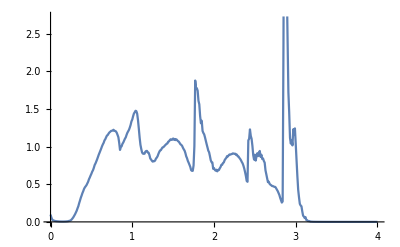

```mathematica
ListPlot[%187,Joined->True]
```

```mathematica
Import["11imp7.csv"]
```

{{0.,0.00802228},{0.01,0.00634194},{0.02,0.00541625},{0.03,0.00433371},{0.04,0.00384118},{0.05,0.00320464},{0.06,0.00271204},{0.07,0.00239821},{0.08,0.00203109},{0.09,0.00179745},{0.1,0.00171148},{0.11,0.00158548},{0.12,0.00161162},{0.13,0.00157653},{0.14,0.001744},{0.15,0.00193893},{0.16,0.00223251},{0.17,0.00263911},{0.18,0.00323229},{0.19,0.00404242},{0.2,0.00523095},{0.21,0.00667621},{0.22,0.00915338},{0.23,0.0135641},{0.24,0.017111},{0.25,0.0343263},{0.26,0.0575907},{0.27,0.0843559},{0.28,0.115289},{0.29,0.148722},{0.3,0.185679},{0.31,0.226057},{0.32,0.271554},{0.33,0.315337},{0.34,0.358072},{0.35,0.401769},{0.36,0.439872},{0.37,0.478679},{0.38,0.512357},{0.39,0.532524},{0.4,0.536151},{0.41,0.535918},{0.42,0.532531},{0.43,0.568362},{0.44,0.610935},{0.45,0.646413},{0.46,0.685311},{0.47,0.729947},{0.48,0.770078},{0.49,0.807076},{0.5,0.843672},{0.51,0.885664},{0.52,0.924135},{0.53,0.968194},{0.54,1.00524},{0.55,1.04687},{0.56,1.07627},{0.57,1.11745},{0.58,1.15031},{0.59,1.18548},{0.6,1.21563},{0.61,1.25162},{0.62,1.28275},{0.63,1.30555},{0.64,1.32625},{0.65,1.34948},{0.66,1.36998},{0.67,1.39488},{0.68,1.40503},{0.69,1.42873},{0.7,1.4298},{0.71,1.44087},{0.72,1.45259},{0.73,1.45522},{0.74,1.45847},{0.75,1.46517},{0.76,1.46396},{0.77,1.45928},{0.78,1.45531},{0.79,1.44994},{0.8,1.44572},{0.81,1.4311},{0.82,1.40403},{0.83,1.36893},{0.84,1.30316},{0.85,1.17561},{0.86,1.21667},{0.87,1.25504},{0.88,1.28526},{0.89,1.31569},{0.9,1.33563},{0.91,1.36408},{0.92,1.40063},{0.93,1.43374},{0.94,1.47885},{0.95,1.51232},{0.96,1.56118},{0.97,1.60575},{0.98,1.66158},{0.99,1.70797},{1.,1.75383},{1.01,1.79212},{1.02,1.84318},{1.03,1.86032},{1.04,1.84164},{1.05,1.78144},{1.06,1.64695},{1.07,1.463},{1.08,1.26652},{1.09,1.1771},{1.1,1.15492},{1.11,1.17083},{1.12,1.19529},{1.13,1.21285},{1.14,1.2221},{1.15,1.20602},{1.16,1.17918},{1.17,1.11785},{1.18,1.07966},{1.19,1.04546},{1.2,1.06023},{1.21,1.0929},{1.22,1.13002},{1.23,1.15928},{1.24,1.2118},{1.25,1.2618},{1.26,1.28174},{1.27,1.32201},{1.28,1.35616},{1.29,1.36927},{1.3,1.40006},{1.31,1.42563},{1.32,1.44662},{1.33,1.47709},{1.34,1.51793},{1.35,1.5387},{1.36,1.56668},{1.37,1.58059},{1.38,1.59345},{1.39,1.61611},{1.4,1.61971},{1.41,1.63235},{1.42,1.63382},{1.43,1.64521},{1.44,1.64504},{1.45,1.64101},{1.46,1.64391},{1.47,1.63691},{1.48,1.63947},{1.49,1.64255},{1.5,1.63656},{1.51,1.62913},{1.52,1.62507},{1.53,1.61895},{1.54,1.60753},{1.55,1.59117},{1.56,1.58192},{1.57,1.57251},{1.58,1.55187},{1.59,1.53862},{1.6,1.5171},{1.61,1.50092},{1.62,1.47632},{1.63,1.44643},{1.64,1.42458},{1.65,1.3928},{1.66,1.36023},{1.67,1.30836},{1.68,1.27976},{1.69,1.23716},{1.7,1.1884},{1.71,1.13051},{1.72,1.05018},{1.73,0.961638},{1.74,0.885315},{1.75,0.816714},{1.76,0.946297},{1.77,2.15265},{1.78,1.96954},{1.79,1.82483},{1.8,1.62682},{1.81,1.50512},{1.82,1.38745},{1.83,1.36201},{1.84,1.34178},{1.85,1.28518},{1.86,1.25225},{1.87,1.22183},{1.88,1.15991},{1.89,1.11203},{1.9,1.00209},{1.91,0.959653},{1.92,0.911884},{1.93,0.889435},{1.94,0.882565},{1.95,0.889943},{1.96,0.904605},{1.97,0.934097},{1.98,0.945438},{1.99,0.989619},{2.,1.03536},{2.01,1.06995},{2.02,1.12011},{2.03,1.15363},{2.04,1.18954},{2.05,1.2122},{2.06,1.22621},{2.07,1.2397},{2.08,1.2571},{2.09,1.27417},{2.1,1.2777},{2.11,1.27517},{2.12,1.28801},{2.13,1.29578},{2.14,1.2953},{2.15,1.30247},{2.16,1.29725},{2.17,1.30108},{2.18,1.30134},{2.19,1.30532},{2.2,1.29475},{2.21,1.29545},{2.22,1.28518},{2.23,1.27558},{2.24,1.27164},{2.25,1.25344},{2.26,1.25362},{2.27,1.23678},{2.28,1.22254},{2.29,1.2067},{2.3,1.19368},{2.31,1.1756},{2.32,1.15968},{2.33,1.1397},{2.34,1.11353},{2.35,1.09005},{2.36,1.04686},{2.37,1.00491},{2.38,0.950627},{2.39,0.872435},{2.4,0.729763},{2.41,0.600404},{2.42,1.20344},{2.43,0.999844},{2.44,0.837069},{2.45,0.84108},{2.46,0.933788},{2.47,0.99626},{2.48,1.08077},{2.49,1.17226},{2.5,1.13246},{2.51,1.06505},{2.52,0.968386},{2.53,0.832592},{2.54,0.782226},{2.55,0.762823},{2.56,0.688641},{2.57,0.673524},{2.58,0.645281},{2.59,0.589496},{2.6,0.598814},{2.61,0.593216},{2.62,0.611672},{2.63,0.621735},{2.64,0.634892},{2.65,0.650421},{2.66,0.660008},{2.67,0.661681},{2.68,0.66913},{2.69,0.666629},{2.7,0.663437},{2.71,0.651545},{2.72,0.646937},{2.73,0.631969},{2.74,0.624738},{2.75,0.614028},{2.76,0.603732},{2.77,0.599678},{2.78,0.592672},{2.79,0.579902},{2.8,0.563368},{2.81,0.544776},{2.82,0.504898},{2.83,0.438569},{2.84,0.340308},{2.85,1.85037},{2.86,1.215},{2.87,0.575978},{2.88,0.511898},{2.89,0.813568},{2.9,0.762945},{2.91,1.23067},{2.92,1.23379},{2.93,1.26718},{2.94,1.04719},{2.95,0.60063},{2.96,0.582914},{2.97,0.226235},{2.98,0.170642},{2.99,0.16917},{3.,0.168959},{3.01,0.139789},{3.02,0.0884625},{3.03,0.0703528},{3.04,0.0379904},{3.05,0.0285108},{3.06,0.010508},{3.07,0.010048},{3.08,0.00581547},{3.09,0.00357091},{3.1,0.0028264},{3.11,0.00214007},{3.12,0.00184411},{3.13,0.00157843},{3.14,0.00137429},{3.15,0.0012147},{3.16,0.00107257},{3.17,0.000935228},{3.18,0.000851737},{3.19,0.000763026},{3.2,0.000682006},{3.21,0.00062223},{3.22,0.000561203},{3.23,0.000503202},{3.24,0.000453151},{3.25,0.000422174},{3.26,0.000391838},{3.27,0.000351993},{3.28,0.000316998},{3.29,0.000293128},{3.3,0.000274871},{3.31,0.000253531},{3.32,0.000234822},{3.33,0.000214278},{3.34,0.000200473},{3.35,0.000187359},{3.36,0.000177426},{3.37,0.000160813},{3.38,0.000149753},{3.39,0.000143157},{3.4,0.000128336},{3.41,0.000119434},{3.42,0.000113853},{3.43,0.000109825},{3.44,0.000100672},{3.45,0.0000940955},{3.46,0.0000886806},{3.47,0.0000815521},{3.48,0.0000776351},{3.49,0.0000727745},{3.5,0.0000684464},{3.51,0.0000648356},{3.52,0.0000624406},{3.53,0.0000584174},{3.54,0.0000552247},{3.55,0.0000517717},{3.56,0.0000496336},{3.57,0.0000456854},{3.58,0.0000445541},{3.59,0.0000414876},{3.6,0.0000391795},{3.61,0.0000374015},{3.62,0.0000349332},{3.63,0.0000336873},{3.64,0.0000323804},{3.65,0.0000296584},{3.66,0.0000284303},{3.67,0.0000271813},{3.68,0.0000256052},{3.69,0.0000240492},{3.7,0.0000232738},{3.71,0.0000219691},{3.72,0.0000214871},{3.73,0.0000196209},{3.74,0.0000192577},{3.75,0.0000178483},{3.76,0.0000178674},{3.77,0.0000164516},{3.78,0.0000163197},{3.79,0.0000152039},{3.8,0.0000144714},{3.81,0.0000137067},{3.82,0.0000132815},{3.83,0.0000124172},{3.84,0.0000120702},{3.85,0.0000114671},{3.86,0.0000109254},{3.87,0.0000106463},{3.88,0.0000100317},{3.89,9.90884×10^-6},{3.9,9.23303×10^-6},{3.91,8.84776×10^-6},{3.92,8.65067×10^-6},{3.93,8.18051×10^-6},{3.94,7.74743×10^-6},{3.95,7.57362×10^-6},{3.96,7.21462×10^-6},{3.97,6.8076×10^-6},{3.98,6.63173×10^-6},{3.99,6.42983×10^-6},{4.,6.23591×10^-6}}

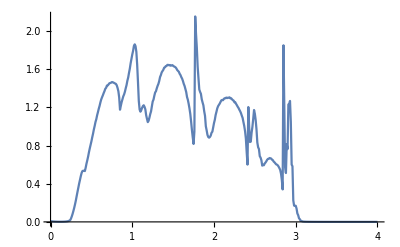

```mathematica
ListPlot[%182,Joined->True]
```

```mathematica
ListPlot[%182,Joined->True]
```

-Graphics-

```mathematica
tr9[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{},A:=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1}(*,{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1}(*,{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];B:=Module[{},η=Module[{gg=g[ω,δ,t,ϵ],P=T1[1]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1}(*,{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl2= Module[{J=sl1},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl3= Module[{J=sl2},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,5}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{11,14}]},ReplacePart[κ,{{μ1,μ1},{μ2,μ2},{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];sl4= Module[{J=sl3},Do[J=Module[{c=RandomChoice[{Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,7}],μ2=RandomInteger[{6,10}],μ3=RandomInteger[{8,14}]},ReplacePart[κ,{{μ1,μ1},(*{μ2,μ2},*){μ3,μ3}}->ω+ⅈ*δ-ϵ1]]]}]},Inverse[IdentityMatrix[14]-c.ConjugateTranspose[P].J.P].c],1];J=J];Il1:=Inverse[IdentityMatrix[14]-sl4.TT[1].SR[ω,δ,1,0].TT[1]].sl4;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].TT[1].sl4.TT[1]].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].TT[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.TT[1].grr1.TT[1]-TT[1].GNON1.TT[1].GNON1]]];η];(A+B)/2]
```

```mathematica
tr9[0,0.001,1,0,1]
```

0.0260336

```mathematica
Export["9imp7.csv",Table[{ω,Mean[Table[tr9[ω,0.001,1,0,0.7],1500]]},{ω,Range[0,4,0.01]}]]
```

9imp7.csv

```mathematica
Import["9imp7.csv"]
```

{{0.,0.0033051},{0.01,0.00259705},{0.02,0.00223955},{0.03,0.00188211},{0.04,0.00166596},{0.05,0.001406},{0.06,0.001306},{0.07,0.00124194},{0.08,0.00119288},{0.09,0.00112087},{0.1,0.00135042},{0.11,0.00142904},{0.12,0.00168459},{0.13,0.00189993},{0.14,0.00232201},{0.15,0.00291118},{0.16,0.00354558},{0.17,0.00443348},{0.18,0.00545061},{0.19,0.00686951},{0.2,0.00925131},{0.21,0.0126825},{0.22,0.0186061},{0.23,0.0319843},{0.24,0.0580936},{0.25,0.144821},{0.26,0.233869},{0.27,0.329262},{0.28,0.402924},{0.29,0.4661},{0.3,0.528224},{0.31,0.571908},{0.32,0.621061},{0.33,0.651002},{0.34,0.684047},{0.35,0.692118},{0.36,0.713494},{0.37,0.7144},{0.38,0.717047},{0.39,0.701708},{0.4,0.681718},{0.41,0.607216},{0.42,0.601437},{0.43,0.7395},{0.44,0.849235},{0.45,0.954739},{0.46,1.04969},{0.47,1.12368},{0.48,1.19479},{0.49,1.26244},{0.5,1.3105},{0.51,1.35773},{0.52,1.39504},{0.53,1.43273},{0.54,1.45859},{0.55,1.48416},{0.56,1.51116},{0.57,1.52595},{0.58,1.54023},{0.59,1.555},{0.6,1.56904},{0.61,1.58361},{0.62,1.59229},{0.63,1.6026},{0.64,1.60984},{0.65,1.61847},{0.66,1.6193},{0.67,1.61985},{0.68,1.62986},{0.69,1.63602},{0.7,1.63545},{0.71,1.63772},{0.72,1.64143},{0.73,1.63678},{0.74,1.63804},{0.75,1.63839},{0.76,1.63539},{0.77,1.63313},{0.78,1.63169},{0.79,1.61979},{0.8,1.61208},{0.81,1.59476},{0.82,1.57546},{0.83,1.52379},{0.84,1.42713},{0.85,1.20499},{0.86,1.37063},{0.87,1.48845},{0.88,1.60809},{0.89,1.70112},{0.9,1.78493},{0.91,1.88841},{0.92,1.94701},{0.93,2.00683},{0.94,2.07375},{0.95,2.11272},{0.96,2.15705},{0.97,2.19836},{0.98,2.22904},{0.99,2.26425},{1.,2.28939},{1.01,2.29282},{1.02,2.31032},{1.03,2.30309},{1.04,2.26329},{1.05,2.20011},{1.06,2.06046},{1.07,1.83947},{1.08,1.6401},{1.09,1.51899},{1.1,1.51476},{1.11,1.5375},{1.12,1.59182},{1.13,1.61984},{1.14,1.63276},{1.15,1.63381},{1.16,1.59216},{1.17,1.57032},{1.18,1.55445},{1.19,1.5297},{1.2,1.54933},{1.21,1.59095},{1.22,1.63789},{1.23,1.66884},{1.24,1.72976},{1.25,1.76567},{1.26,1.78958},{1.27,1.83471},{1.28,1.85539},{1.29,1.87366},{1.3,1.90221},{1.31,1.91897},{1.32,1.94409},{1.33,1.96142},{1.34,1.98075},{1.35,2.01264},{1.36,2.02133},{1.37,2.028},{1.38,2.04646},{1.39,2.054},{1.4,2.05217},{1.41,2.07181},{1.42,2.06944},{1.43,2.07252},{1.44,2.07297},{1.45,2.07977},{1.46,2.07906},{1.47,2.06801},{1.48,2.07244},{1.49,2.06231},{1.5,2.05372},{1.51,2.05293},{1.52,2.03777},{1.53,2.02361},{1.54,2.02879},{1.55,2.00139},{1.56,1.99616},{1.57,1.97501},{1.58,1.95433},{1.59,1.95255},{1.6,1.93495},{1.61,1.92027},{1.62,1.90391},{1.63,1.89095},{1.64,1.87326},{1.65,1.84869},{1.66,1.83069},{1.67,1.79195},{1.68,1.75863},{1.69,1.69941},{1.7,1.64378},{1.71,1.5555},{1.72,1.45561},{1.73,1.35274},{1.74,1.26543},{1.75,1.10707},{1.76,1.00361},{1.77,1.67341},{1.78,1.77592},{1.79,1.98366},{1.8,1.8075},{1.81,1.83487},{1.82,1.64007},{1.83,1.67814},{1.84,1.57333},{1.85,1.57169},{1.86,1.46581},{1.87,1.4455},{1.88,1.39312},{1.89,1.24997},{1.9,1.15729},{1.91,1.08191},{1.92,1.11316},{1.93,1.16929},{1.94,1.17211},{1.95,1.18723},{1.96,1.2024},{1.97,1.24352},{1.98,1.29437},{1.99,1.33997},{2.,1.36331},{2.01,1.39572},{2.02,1.42462},{2.03,1.43185},{2.04,1.44484},{2.05,1.45941},{2.06,1.46417},{2.07,1.47529},{2.08,1.47696},{2.09,1.4733},{2.1,1.47795},{2.11,1.48168},{2.12,1.47364},{2.13,1.47118},{2.14,1.47104},{2.15,1.47069},{2.16,1.46889},{2.17,1.47004},{2.18,1.47033},{2.19,1.46664},{2.2,1.47076},{2.21,1.47065},{2.22,1.47343},{2.23,1.47877},{2.24,1.47618},{2.25,1.47573},{2.26,1.47352},{2.27,1.47691},{2.28,1.46596},{2.29,1.43787},{2.3,1.42988},{2.31,1.39488},{2.32,1.36262},{2.33,1.31103},{2.34,1.254},{2.35,1.19407},{2.36,1.15093},{2.37,1.09444},{2.38,1.03409},{2.39,0.960411},{2.4,0.842152},{2.41,0.669258},{2.42,1.08273},{2.43,1.30751},{2.44,1.41602},{2.45,1.33027},{2.46,1.24517},{2.47,1.1996},{2.48,1.44512},{2.49,1.44957},{2.5,1.24744},{2.51,1.32443},{2.52,1.14761},{2.53,1.07938},{2.54,1.19794},{2.55,0.801695},{2.56,0.680879},{2.57,0.627391},{2.58,0.628526},{2.59,0.648424},{2.6,0.662558},{2.61,0.675907},{2.62,0.695447},{2.63,0.714722},{2.64,0.72712},{2.65,0.738303},{2.66,0.75647},{2.67,0.770768},{2.68,0.775051},{2.69,0.791391},{2.7,0.785256},{2.71,0.790757},{2.72,0.773345},{2.73,0.750735},{2.74,0.715328},{2.75,0.665769},{2.76,0.621834},{2.77,0.568171},{2.78,0.522811},{2.79,0.474321},{2.8,0.431011},{2.81,0.386377},{2.82,0.32608},{2.83,0.262924},{2.84,0.178026},{2.85,0.966944},{2.86,2.15756},{2.87,2.48134},{2.88,2.68366},{2.89,1.77521},{2.9,1.45285},{2.91,2.21951},{2.92,0.88103},{2.93,2.84716},{2.94,1.60001},{2.95,1.15676},{2.96,1.05037},{2.97,0.467417},{2.98,0.155889},{2.99,0.407058},{3.,0.0656898},{3.01,0.0979992},{3.02,0.0264641},{3.03,0.0163442},{3.04,0.0103738},{3.05,0.00602472},{3.06,0.00456795},{3.07,0.00326221},{3.08,0.00277856},{3.09,0.00241912},{3.1,0.00208696},{3.11,0.00171068},{3.12,0.00155165},{3.13,0.00136347},{3.14,0.00120355},{3.15,0.00104962},{3.16,0.000960674},{3.17,0.000858343},{3.18,0.000764306},{3.19,0.000713625},{3.2,0.000604469},{3.21,0.000567818},{3.22,0.000513633},{3.23,0.00046419},{3.24,0.000425969},{3.25,0.000384595},{3.26,0.000357797},{3.27,0.000323502},{3.28,0.000304398},{3.29,0.000286822},{3.3,0.000256102},{3.31,0.000243147},{3.32,0.00022},{3.33,0.000197035},{3.34,0.000191502},{3.35,0.000176422},{3.36,0.000155577},{3.37,0.000152689},{3.38,0.00013941},{3.39,0.000130873},{3.4,0.000119333},{3.41,0.000117373},{3.42,0.000101923},{3.43,0.0000996154},{3.44,0.0000936034},{3.45,0.0000884311},{3.46,0.0000796797},{3.47,0.0000769275},{3.48,0.0000753854},{3.49,0.0000695319},{3.5,0.0000631956},{3.51,0.0000614439},{3.52,0.0000561041},{3.53,0.0000535012},{3.54,0.0000530671},{3.55,0.0000483835},{3.56,0.00004498},{3.57,0.0000437646},{3.58,0.0000411638},{3.59,0.0000392025},{3.6,0.0000381129},{3.61,0.0000360811},{3.62,0.0000335585},{3.63,0.0000313618},{3.64,0.000030219},{3.65,0.0000283275},{3.66,0.0000278304},{3.67,0.0000261049},{3.68,0.0000243096},{3.69,0.0000230007},{3.7,0.0000217929},{3.71,0.0000213343},{3.72,0.0000198302},{3.73,0.000019751},{3.74,0.0000178357},{3.75,0.0000173515},{3.76,0.0000169063},{3.77,0.000015834},{3.78,0.000015245},{3.79,0.0000146593},{3.8,0.0000136827},{3.81,0.0000134074},{3.82,0.000012907},{3.83,0.0000118407},{3.84,0.000011555},{3.85,0.0000111173},{3.86,0.0000110023},{3.87,9.94225×10^-6},{3.88,9.33327×10^-6},{3.89,9.39663×10^-6},{3.9,8.69892×10^-6},{3.91,8.39028×10^-6},{3.92,8.11034×10^-6},{3.93,8.20512×10^-6},{3.94,7.4891×10^-6},{3.95,7.10577×10^-6},{3.96,6.93271×10^-6},{3.97,6.54368×10^-6},{3.98,6.37626×10^-6},{3.99,6.29885×10^-6},{4.,6.06477×10^-6}}

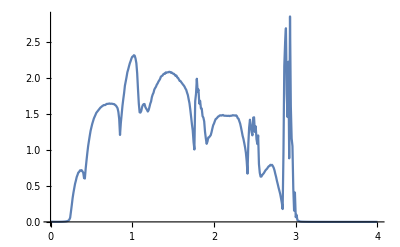

```mathematica
ListPlot[%200,Joined->True]
```